```mathematica
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
SetDirectory[NotebookDirectory[]]
```

/home/kirscher/kette_repo/limit_cycles/manuscript/graphs

```mathematica
hbarc=197.327053;
Mm=938.858;
m1=2 Mm;m2=2 Mm;
μ=m1 m2/(m1+m2);
mh2=(2 μ)/(hbarc)^2;
Print["ℏ^2/(2  μ) = ",1/mh2]
cijTh=10^-12;
dbg=False;
```

ℏ^2/(2  μ) = 20.7369

Read LEC list (e.g. fitted to two-body scattering length via <<<Fit_Scattering_length.nb>>>)

```mathematica
activeLEC=Select[Import["/home/kirscher/Documents/vault/Vorlesungen/num_methods/lec_ex0_b2.22.dat","Table"][[2;;]],#[[3]]!=-1.&];
activeLEC=activeLEC[[;;;;11]]
```

{{8.,-974.194,-1105.1,0.},{19.,-2243.04,-1748.02,4.36},{30.,-3499.32,-1964.75,0.},{41.,-4750.43,-1916.56,0.}}

```mathematica
(*one dimer to rule them all*)
eCore=2.2;
ScaleFac=1.;
dimerCore=Get["UnivDimerWFI"]
dimerCore=Transpose[{dimerCore[[All,1]],ScaleFac dimerCore[[All,2]]}]
```

{{0.0875605,0.159053},{0.0841116,0.0152572}}

{{0.0875605,0.159053},{0.0841116,0.0152572}}

Calculate the dimer wave function in a Gaussian basis rdimer=∑_(i=1)^N c_i·e^(-α_i r^2)

```mathematica
RiccatiBesselJ=Compile[{z,l},z SphericalBesselJ[l,z]];
RiccatiBesselN=Compile[{z,l},(-1)^l z SphericalBesselY[l,z]];
```

```mathematica
(*Boundery conditions for the wavefunction*)
alpha=Compile[{ra,ka,la,ha},RiccatiBesselN[ka (ra+ha),la]/RiccatiBesselN[ka ra,la]];

beta=Compile[{rb,kb,lb,hb},RiccatiBesselJ[kb (rb+hb),lb]-RiccatiBesselJ[kb rb,lb] (RiccatiBesselN[kb (rb+hb),lb]/RiccatiBesselN[kb rb,lb])];
```

reference: J. Spanier, K.B. Oldham - An Atlas of Functions (1987)

x·j_n(x)=√((π x)/2)J_(n+1/2)(x)=^(x∈C)√((π x)/2)i^(n+1/2) I_(n+1/2)(Re[x])
with
 j_n: spherical Bessel (1st kind)
 J_n: Bessel (1st kind)
 I_n: modified Bessel (1st kind)
 to optimize runtime, we substitute in this implementation -- valid for S-wave scattering, only:
 j_0(i x)=Sinh[x]/x=1/x (e^x-e^-x)/2
 and
 j_1(i x)=i x^-1(Cosh[x]-Sinh[x]/x)
 For numerical stability at arguments x>>1, it is curucial to subsitute the following representation:
 e^(-aR^2-bR'^2) Sinh[bRR']=1/2(e^(-aR^2-bR'^2+bRR')-e^(-aR^2-bR'^2-bRR')) and similarly for the hyperbolic cosine;
 Retaining the Sinh built-in function throws, at best, warnings, and yields significantly inaccurate and almost certainly non-sensical results!

```mathematica
NormTF=Compile[{{core,_Real,2}},Total[Flatten[Table[core[[i]][[1]] core[[j]][[1]] core[[k]][[1]] core[[l]][[1]] (1/2^(7/2)) (Pi/((core[[i]][[2]]+core[[j]][[2]]) (core[[k]][[2]]+core[[l]][[2]])))^(3/2),{i,Length[core]},{j,Length[core]},{k,Length[core]},{l,Length[core]}]]]];


VlocTF=Compile[{r,lam,Cc,Dd,Aa,Bb,Gg,Hh},Block[{eta2,eta3,w2,w3},
eta2=(π^(3/2)/4) Cc/(lam Bb + Aa(lam + 2Gg +2  Bb) + lam Hh +2 Bb Hh+Gg(lam +2Hh))^(3/2);
w2= 2lam(Aa+Hh)(Gg+Bb)/(lam Bb + Aa(lam+2 Gg+2Bb)+lam Hh +2 Bb Hh+Gg(lam+2Hh));
eta3 =(π^(3/2)/4) Cc/(lam Bb + Gg(lam + 2Bb)+lam Hh +2Bb Hh + Aa(lam+2Gg+2Hh))^(3/2);
w3 = 2lam(Aa+Bb)(Gg+Hh)/(lam Bb + Gg(lam+2Bb)+lam Hh +2Bb Hh+Aa(lam+2Gg+2Hh));
eta2 Exp[-w2 r^2]+eta3 Exp[-w3 r^2]
]];

WnolocTF3=Compile[{r,rp,Ee,lam,Cc,Dd,Aa,Bb,Gg,Hh,Ll,TwoMyOverHBsq},Block[{zeta1,zeta2,zeta3,a1,b1,c1,a2,b2,c2,a3,b3,c3,Sinh1,Sinh2,Sinh3,ex1,ex2,ex3,CoshA},
zeta1=-(π^(3/2)/(√2)) 1/(Aa+Bb+Gg+ Hh)^(3/2) (1/TwoMyOverHBsq);
a1=(4Bb Hh + Gg Bb+Gg Hh+Aa Bb +Aa Hh)/(2Aa+2Bb+2Gg+2Hh);
b1=(2Gg Bb -2Gg Hh -2 Aa Bb +2 Aa Hh)/(2Aa+2Bb+2Gg+2Hh);
c1=(Gg Bb +Hh Gg+4Aa Gg +Aa Bb +Aa Hh)/(2Aa+2Bb+2Gg+2Hh);

zeta2=-(π^(3/2)/(√2)) Cc/(2lam+Aa +Bb+ Gg+Hh)^(3/2);
zeta3=-(π^(3/2)/(√2)) Cc/(2lam+Aa +Bb+ Gg+Hh)^(3/2);

a2=(4Hh(2lam+Bb)+Gg(2lam +Bb+Hh)+Aa(2lam+Bb+Hh))/(2(2 lam+Aa+Bb+Gg+Hh));
b2=(Gg(4 lam+2 Bb-2 Hh)+Aa (-4 lam-2 Bb+2 Hh))/(2 (2 lam+Aa+Bb+Gg+Hh));
c2=( Gg(2lam+Bb+Hh)+Aa(2lam+4Gg+Bb+Hh))/(2(2 lam+Aa+Bb+Gg+Hh));

a3= (4Bb(2lam+Hh)+Gg(Bb+2lam+Hh)+Aa(2lam+Bb+Hh))/(2(2 lam+Aa+Bb+Gg+Hh));
b3=(Gg(2Bb-4lam-2Hh)+Aa(4lam+2Hh-2Bb))/(2(2 lam+Aa+Bb+Gg+Hh));
c3=(Gg(Bb+2lam+Hh)+Aa(4Gg+2lam+Bb+Hh))/(2(2 lam+Aa+Bb+Gg+Hh));

(* these conditions avoid having to multiply a Gaussian whose argument is larger than that of a Sinc with the
latter which amounts only to a numerical zero; if we assume any number <= 10^-14 to be zero, numRAD ≈ 217 *)

Sinh1=If[b1==0,r rp,(Exp[b1 r rp]-Exp[-b1 r rp])/(2 b1)];
Sinh2=If[b2==0,r rp,(Exp[b2 r rp]-Exp[-b2 r rp])/(2 b2)];
Sinh3=If[b3==0,r rp,(Exp[b3 r rp]-Exp[-b3 r rp])/(2 b3)];
(*ex1=If[(-a1 r^2-c1 rp^2)<-20,0,Exp[-a1 r^2-c1 rp^2]];
ex2=If[(-a2 r^2-c2 rp^2)<-20,0,Exp[-a2 r^2-c2 rp^2]];
ex3=If[(-a3 r^2-c3 rp^2)<-20,0,Exp[-a3 r^2-c3 rp^2]];*)
ex1=Exp[-a1 r^2-c1 rp^2];
ex2=Exp[-a2 r^2-c2 rp^2];
ex3=Exp[-a3 r^2-c3 rp^2];

(-4 Pi) (zeta1 ex1 ((-(4 a1^2 r^2+b1^2 rp^2-2 a1)- TwoMyOverHBsq Ee) Sinh1+2/(√3) a1 b1 (r rp (Exp[b1 r rp]+Exp[-b1 r rp])-0.5 Sinh1))+zeta2 Sinh2 ex2+zeta3 Sinh3 ex3)
]];
```

```mathematica
SolveSecularP3[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,d0_?NumberQ,a00_?ArrayQ,TwoMyOverHBsq_?NumberQ]:=Block[{hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,wf,tanDelta,usol,energyMeV,nff,cij},
t1=AbsoluteTime[];
hDif=Rdis/Npoints;
energyMeV=(momentum^2)/TwoMyOverHBsq;
Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{Npoints,Npoints}];

normsqu=1/NormTF[a00];

Wmats={};
SetSharedVariable[Wmats];

ParallelDo[

cij=a00[[ii]][[1]] a00[[jj]][[1]] a00[[kk]][[1]]  a00[[ll]][[1]] normsqu;

amat=DiagonalMatrix[Table[-hDif^2 TwoMyOverHBsq VlocTF[i hDif,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],a00[[kk]][[2]],a00[[ll]][[2]]],{i,1,Npoints}]];

wmat=Table[-hDif^3 TwoMyOverHBsq WnolocTF3[i hDif,j hDif,energyMeV,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],a00[[kk]][[2]],a00[[ll]][[2]],Lin,TwoMyOverHBsq],{i,1,Npoints},{j,1,Npoints}(*,ProgressReporting->False*)]; 

AppendTo[Wmats,cij (amat+wmat)];
(*AppendTo[Wmats,cij amat];*)

,{ii,1,Length[a00]},{jj,1,Length[a00]},{kk,1,Length[a00]},{ll,1,Length[a00]}];

Wmat=Total[Wmats];
Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2),{i,1,Npoints}]];

Amat=Kmat+Dmat+Wmat;

bcol=ConstantArray[0,Npoints];
ucol=Array[Subscript["u", ##]&,{Npoints}];

bcol⟦-1⟧=- beta[Rdis,momentum,Lin,hDif];
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[Rdis,momentum,Lin,hDif];

usol=LinearSolve[Amat,bcol];
relerr=Norm[Amat.usol-bcol]/Norm[usol];
(*Print["relative error in wave-function solution = ",relerr];*)

(*tanDelta= (RiccatiBesselJ[momentum Rdis,Lin]/RiccatiBesselN[momentum Rdis,Lin])-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin]);*)
sol=NSolve[usol⟦-1⟧==RiccatiBesselJ[momentum Rdis,Lin]-RiccatiBesselN[momentum Rdis,Lin] xx,xx,Reals];
tanDelta=xx/.sol[[-1]];
t2=AbsoluteTime[];
(*Print["finite-difference runtime Δt = ",(t2-t1)/60.," mins     p_match·r_max = ",momentum Rdis];*)
{tanDelta,usol}
];
```

```mathematica
GetEREP3[l_,rMax_,nPoints_,core_,LECc_,energ_:0.001]:=Module[{locall=l},
LECd=0.0;
momFM=Sqrt[mh2 energ];
{TanDelSwave,wfkt}=SolveSecularP3[rMax,nPoints,momFM,0,locall,LECc,LECd,core,mh2];
{-TanDelSwave/Sqrt[mh2 energ ],wfkt}
]
```

alternative to the stochastic and inefficient search for an appropriate basis, one can invoke a genetic optimization (external Python/Fortran program, look for <bridgeA2_tmp.py> and calls therein)
and feed the results to the function <CalcDimerE[]> (see above

Using λ=8.fm^-2     C=-974.194MeV  which is renormalized to B(dimer)=2.2MeV

kinetic-energy pre-factor:  1.21686

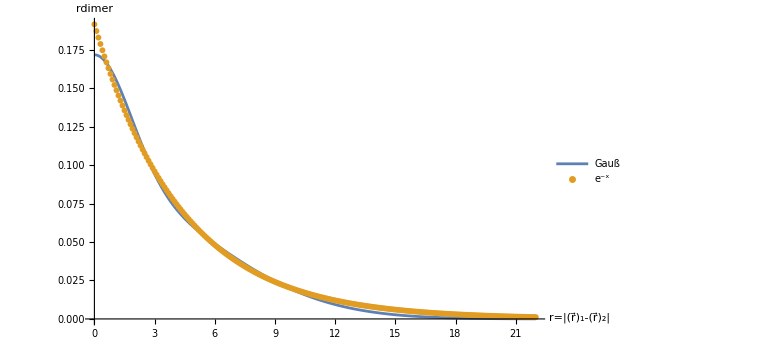

```mathematica
lambdas=activeLEC[[All,1]];
lambdaTest=lambdas[[1]];
LECc=Flatten[Select[activeLEC,#[[1]]==lambdaTest&]][[2]];
Print["Using λ=",Style[lambdaTest,Red],"fm^-2     C=",Style[LECc,Red],"MeV  which is renormalized to B(dimer)=",Style[eCore,Red],"MeV"];

JacobiTrailWavefunctionU=Total[#[[1]] Exp[-#[[2]] r1^2]&/@dimerCore];rR=Range[0,22,0.100];
JacobiTrailWavefunctionDataU=Table[JacobiTrailWavefunctionU/.{r1->R1},{R1,rR}];

plotData=Transpose[{rR,JacobiTrailWavefunctionDataU}];
plotDataExp=Table[{rr,√((√(Mm eCore))/(2 π hbarc))Exp[-(√(Mm eCore))/hbarc rr]},{rr,rR}];
lgd={"Gauß","e^-x"};
Print["kinetic-energy pre-factor:  ",NormTF[dimerCore]];

ListPlot[{Transpose[{rR,plotData[[All,2]]}],Transpose[{rR,plotDataExp[[All,2]]}]},AxesLabel->{"r=|(r⃗)_1-(r⃗)_2|","TemplateBox[{\"r\", \"dimer\"},\"BraKet\"]"},PlotLegends->lgd,ImageSize->Large,PlotLabels->Automatic,Joined->{True,False}]
```

```mathematica
(* energy at which the scattering length is obtained from the amplitude *)
energ=0.01;
(* Integration grid *)
rMa=12;
grdPerFermi=13;
nGrd=IntegerPart[rMa grdPerFermi];
results={};

Do[

LECc=Flatten[Select[activeLEC,#[[1]]==lam&]][[2]];

tmp=GetEREP3[lam,rMa,nGrd,dimerCore,LECc,energ][[1]];
AppendTo[results,{lam,LECc,rMa,nGrd,eCore,tmp,tmp/(hbarc/√(Mm Abs[eCore]))}];
Print["λ=",lam," B(2)=",eCore,"  C_0(λ)=",LECc,")  ; R_max=",rMa," ; #=",nGrd," ; E_match=",energ," ; a_dd=",tmp," ; a_dd/a_aa=",tmp/(hbarc/√(Mm Abs[eCore]))];
,{lam,lambdas}];
```

λ=8. B(2)=2.2  C_0(λ)=-974.194)  ; R_max=12 ; #=156 ; E_match=0.01 ; a_dd=8.64722 ; a_dd/a_aa=1.9916

λ=19. B(2)=2.2  C_0(λ)=-2243.04)  ; R_max=12 ; #=156 ; E_match=0.01 ; a_dd=8.87277 ; a_dd/a_aa=2.04354

λ=30. B(2)=2.2  C_0(λ)=-3499.32)  ; R_max=12 ; #=156 ; E_match=0.01 ; a_dd=9.07324 ; a_dd/a_aa=2.08972

λ=41. B(2)=2.2  C_0(λ)=-4750.43)  ; R_max=12 ; #=156 ; E_match=0.01 ; a_dd=9.18649 ; a_dd/a_aa=2.1158

### maximal-integration-range dependence of the a_dd scattering-length pre/post-diction

λ = 8.   C_0(λ) = -974.194     R_max = 12     #(grid points) = 180                a_dd = 8.6456 fm        a_dd/a_aa = 1.99122

λ = 19.   C_0(λ) = -2243.04     R_max = 12     #(grid points) = 180                a_dd = 8.87121 fm        a_dd/a_aa = 2.04318

λ = 30.   C_0(λ) = -3499.32     R_max = 12     #(grid points) = 180                a_dd = 9.07157 fm        a_dd/a_aa = 2.08933

λ = 41.   C_0(λ) = -4750.43     R_max = 12     #(grid points) = 180                a_dd = 9.18476 fm        a_dd/a_aa = 2.1154

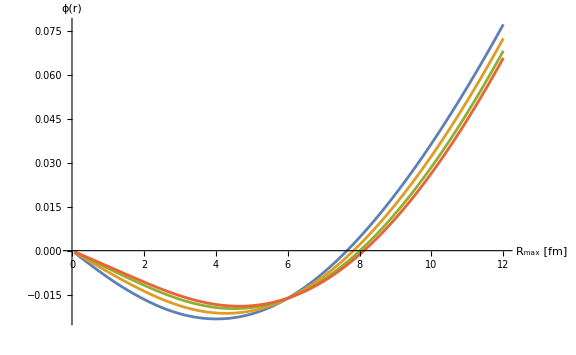

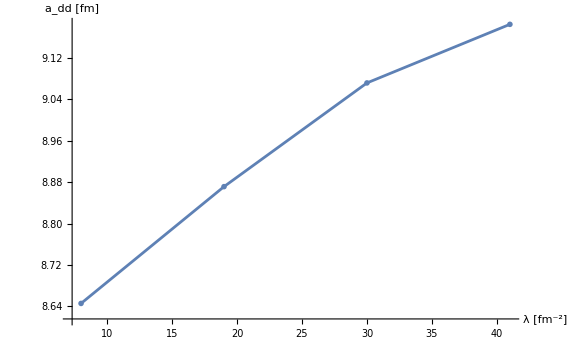

```mathematica
grdPerFermi=15;
rMax=12;
nGrd=IntegerPart[rMax grdPerFermi];
Grd=Range[0,rMax,1/grdPerFermi][[2;;]];

results={};
resultsWF={};
runtimes={};

(*SetSharedVariable[results,resultsPhases];*)
Do[

LECc=Flatten[Select[activeLEC,#[[1]]==lam&]][[2]];
ta=AbsoluteTime[];
{tmp,tmp2}=GetEREP3[lam,rMax,nGrd,dimerCore,LECc,energ];
tb=AbsoluteTime[];
AppendTo[results,tmp];
AppendTo[resultsWF,Transpose[{Grd,tmp2}]];
AppendTo[runtimes,{rMa,(tb-ta)/60.}];
Print["λ = ",lam,"   C_0(λ) = ",LECc,"     R_max = ",rMax,"     #(grid points) = ",nGrd,"                a_dd = ",tmp," fm        a_dd/a_aa = ",Style[tmp/(hbarc/√(Mm Abs[eCore])),Red,18]];
,{lam,lambdas}]

ListPlot[resultsWF,Joined->True,PlotRange->Full,ImageSize->Large,AxesLabel->{"R_max [fm]","ϕ(r)"}]
ListPlot[Transpose[{lambdas,results}],Joined->True,PlotMarkers->"OpenMarkers",AxesLabel->{"λ [fm^-2]","a_dd [fm]"}]
```

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

a_dd = 8.52747     a_dd/a_aa = 1.96401

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

a_dd = 8.74882     a_dd/a_aa = 2.015

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

a_dd = 8.94601     a_dd/a_aa = 2.06041

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

a_dd = 9.05768     a_dd/a_aa = 2.08613

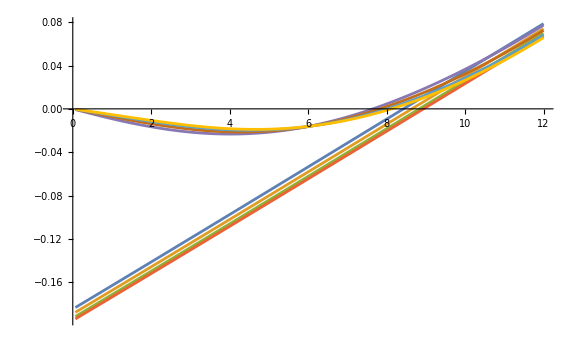

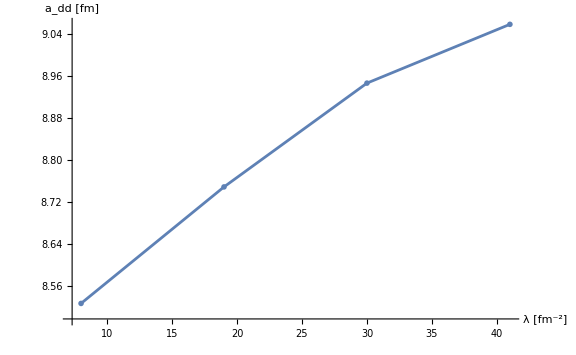

```mathematica
momFM=Sqrt[mh2 energ];
rRan=Range[0,rMax,1/grdPerFermi];
match1=1;
match2=5;
resultsadd={};
riccatis={};
Do[

sol=NSolve[{resultsWF[[nres]][[All,2]][[-match1]]==nm (RiccatiBesselJ[momFM (rMax-match1/grdPerFermi),0]-tandd RiccatiBesselN[momFM (rMax-match1/grdPerFermi),0]),
resultsWF[[nres]][[All,2]][[-match2]]==nm (RiccatiBesselJ[momFM (rMax-match2/grdPerFermi),0]-tandd RiccatiBesselN[momFM (rMax-match2/grdPerFermi),0])},{nm,tandd},Reals];

RiccatiBJN=Table[(nm (RiccatiBesselJ[momFM r,0]-tandd RiccatiBesselN[momFM r,0])),{r,rRan}];
RiccatiBJN=RiccatiBJN/.sol[[1]];
AppendTo[riccatis,Transpose[{rRan,RiccatiBJN}]];

add=(-tandd/.sol[[1]][[2]])/Sqrt[mh2 energ ];
AppendTo[resultsadd,add];

Print["a_dd = ",add, "     a_dd/a_aa = ",add/(hbarc/√(Mm Abs[eCore])) ]
,{nres,Range[Length[lambdas]]}]
ListPlot[Join[riccatis,resultsWF],Joined->True,PlotRange->Full,ImageSize->Large]
ListPlot[Transpose[{lambdas,resultsadd}],Joined->True,PlotMarkers->"OpenMarkers",AxesLabel->{"λ [fm^-2]","a_dd [fm]"}]
```